```mathematica
Quit[];
```

```mathematica
(*TFIIA Induction Data*)
inductionData = {{0,0}, {10, 0.0}, {20,0.00807255}, {25, 0.041814517}, {30, 0.134598958}, {40,0.236474998}, {60,0.4433163}, {90,0.908601116 },{120,1.0}};
```

```mathematica
inductionFit=NonlinearModelFit[inductionData,X*((t/t0)^3/((t/t0)^3+1)),{X,t0},t];
```

```mathematica
%2
```

FittedModel[(3.94583×10^-6 t^3)/(1+3.26249×10^-6 t^3)]

```mathematica
%3["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
X | 1.20945 | 0.0602507 | 20.0737 | 1.90596×10^-7
t0 | 67.4244 | 3.48501 | 19.347 | 2.45721×10^-7

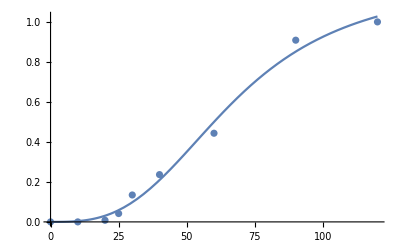

```mathematica
Show[{Plot[Normal[inductionFit[t]],{t,0,120}],ListPlot[inductionData]}]
```

```mathematica
time = {10,20,25,30,40,60,90,120};
```

```mathematica
ratioData = Import["/Users/sb3de/Box Sync/stefan/projects/TF-Chromatin_Dynamics/Competition_ChIP_Bekiranov/competition_ChIP/TFIIA/Normalized_Ratio_Data/tfiia_ratioCountTable_readDepth_and_western_normalized_no_head.txt","Table"];
```

```mathematica
Sites=Length[ratioData];
```

```mathematica
cBSat=inductionFit["BestFitParameters"][[1]][[2]];
```

```mathematica
t0=inductionFit["BestFitParameters"][[2]][[2]];
```

```mathematica
cB[t_]=cBSat*((t/t0)^3/((t/t0)^3+1));
```

```mathematica
modela=ParametricNDSolveValue[{b'[t]==-kd*b[t]+ka*cB[t]*(1-a[t]-b[t]),a'[t]==-kd*a[t]+ka*(1-a[t]-b[t]),a[0]==ka/(ka+kd),b[0]==0},a,{t,0,120},{ka,kd}];
```

```mathematica
modelb=ParametricNDSolveValue[{b'[t]==-kd*b[t]+ka*cB[t]*(1-a[t]-b[t]),a'[t]==-kd*a[t]+ka*(1-a[t]-b[t]),a[0]==ka/(ka+kd),b[0]==0},b,{t,0,120},{ka,kd}];
```

```mathematica
inductionModel[X_,t1_,t_]=X*((t/t1)^3/((t/t1)^3+1));
```

```mathematica
TestList ={};
```

```mathematica
AppendTo[TestList,{"Site","t1 [min]","t1_Error [min]","t1_p-value","Hill_Model_RSquared","t1/2 [min]","kd [1/min]","kd_Error [1/min]","kd_p-value","Turnover_Model_RSquared"}];
```

```mathematica
For[i=1,i≤Sites,i++, 
ratioDataTemp = ratioData[[i,2;;9]]; 
dataToFitPreScaled={time,ratioDataTemp}//Transpose;inductionFitToData = NonlinearModelFit[dataToFitPreScaled, {inductionModel[X,t1,t]+B,X>0,t1>0,B>0},{{X,ratioDataTemp[[8]]-ratioDataTemp[[1]]},{t1,72.3},{B,ratioDataTemp[[1]]}},t,MaxIterations->100]; ampTemp=inductionFitToData["BestFitParameters"][[1]][[2]];t1Temp=inductionFitToData["BestFitParameters"][[2]][[2]];backTemp=inductionFitToData["BestFitParameters"][[3]][[2]];ratioDataBackSubTemp = ratioDataTemp - backTemp;scaleFactor = cBSat/ampTemp;dataToFitTemp={time,scaleFactor*ratioDataBackSubTemp}//Transpose;t1ErrorTemp=inductionFitToData["ParameterErrors"][[2]];t1Pvalue=inductionFitToData["ParameterPValues"][[2]];t1RSquared =inductionFitToData["RSquared"];If[t1Temp>t0 &&t1RSquared>0.7 && ampTemp > 0,
resTimeInit =0.607*(t1Temp-t0)+0.201;
kdEst = Log[2]/resTimeInit;
kaEst=kdEst;turnoverModel=NonlinearModelFit[dataToFitTemp,modelb[ka,kd][t]/modela[ka,kd][t],{{ka,kaEst},{kd,kdEst}},t,MaxIterations->100];kdTemp=turnoverModel["BestFitParameters"][[2]][[2]];resTimeTemp=Log[2]/kdTemp;kdErrorTemp=turnoverModel["ParameterErrors"][[2]];kdPvalueTemp=turnoverModel["ParameterPValues"][[2]];kdRSquared=turnoverModel["RSquared"];AppendTo[TestList,{ratioData[[i,1]],t1Temp,t1ErrorTemp,t1Pvalue,t1RSquared,resTimeTemp,kdTemp,kdErrorTemp,kdPvalueTemp,kdRSquared}]; ,AppendTo[TestList,{ratioData[[i,1]],t1Temp,t1ErrorTemp,t1Pvalue,t1RSquared,"NA","NA","NA","NA","NA"}];];];
```

```mathematica
Export["/Users/sb3de/test/TFIIA_Turnover_Model_RD_Western_Norm_RSqr70Pct_Exact_Init.tsv",TestList];
```